## Cellular Potts Model (CPM)

### params

```mathematica
(* adhesion strength *)
Subscript[j, 00]= 0;Subscript[j, 11]=6;Subscript[j, 22]=6;
Subscript[j, 01]=Subscript[j, 10]=6;
Subscript[j, 02]=Subscript[j, 20]=6;
Subscript[j, 12]=Subscript[j, 21]=16;

J[0,0]=Subscript[j, 00];J[1,1]=Subscript[j, 11];J[2,2]=Subscript[j, 22];
J[1,0]=Subscript[j, 10];J[0,1]=Subscript[j, 01];
J[2,0]=Subscript[j, 20];J[0,2]=Subscript[j, 02];
J[1,2]=Subscript[j, 12];J[2,1]=Subscript[j, 21];

JMatrix=({{Subscript[j, 00], Subscript[j, 01], Subscript[j, 02]}, {Subscript[j, 10], Subscript[j, 11], Subscript[j, 12]}, {Subscript[j, 20], Subscript[j, 21], Subscript[j, 22]}});
```

```mathematica
MatrixForm[Map[Style[#,{GrayLevel[0.5RandomReal[]],FontSize->30}]&,JMatrix,{2}]]
```

(0 | 6 | 6
6 | 6 | 16
6 | 16 | 6)

```mathematica
Kparam=<|
0-><|ka-> 0,kp->0,a0-> 0,p0->0|>, 
1-><|ka-> 1,kp->2,a0-> 100,p0->1|>,
2-><|ka-> 1,kp->2,a0->100,p0-> 1|>
|>; (*parameters*)

T=10;(*temperature*)

n=100; (* canvas size *)
A=ConstantArray[0,{n,n}];(* empty canvas *)
MCSiter=50; (* number of iterations *)
```

### Data structures

```mathematica
boundaryPts=CreateDataStructure["HashSet"]
```

DataStructure[HashSet, {Data -> {}}]

```mathematica
ls=CreateDataStructure["DynamicArray"]
```

DataStructure[DynamicArray, {Data -> {}}]

### f(x)

```mathematica
(* cross and moore neighbour indices within bounds of the canvas *)
crossneighbours[{p_,q_}]:=DeleteCases[{
{p,q-1},
{p,q+1},
{p-1,q},
{p+1,q}},{OrderlessPatternSequence[x_/;x≤0||x>n,_]},{1}];

mooreneighbours[{p_,q_}]:=DeleteCases[{
{p,q-1},
{p,q+1},
{p-1,q-1},
{p-1,q},
{p-1,q+1},
{p+1,q-1},
{p+1,q},
{p+1,q+1}},{OrderlessPatternSequence[x_/;x≤0||x>n,_]},{1}];
```

```mathematica
Clear@fun;
Block[{z},
fun=Function[x,
Which[Length[z=Union@Extract[spCellArrU,mooreneighbours@x]]>1,x,
Length[z]==1&&(Complement[z,{spCellArrU[[Sequence@@x]]}])≠{},x,
True,Nothing]
]
];
```

```mathematica
updateBoundaryPts[CellId_,targetPt_]:=Block[{neighbours,nid},
If[CellId==0,
If[boundaryPts["MemberQ",targetPt],boundaryPts["Remove",targetPt]]
];
Scan[
(nid=spCellArrU[[Sequence@@#]];
If[(nid≠0)&&(Length[Union@Flatten@Extract[spCellArrU,mooreneighbours@#]]>1),
If[Not@boundaryPts["MemberQ",#],boundaryPts["Insert",#]]
])&,mooreneighbours[targetPt]
];
];
```

```mathematica
cellPerimeterUpdate[prevID_,newID_,neighbourPts_]:=Block[{nnew=0,nold=0,nt},
If[prevID==newID,Return[]];
Do[
nt=spCellArrU[[Sequence@@neighbour]];
If[nt≠newID,nnew++];
If[nt≠prevID,nold++];

If[nt≠0,
If[nt==prevID,cellperimeter[nt]++];
If[nt==newID,cellperimeter[nt]--];
],{neighbour,neighbourPts}];

If[prevID≠0,cellperimeter[prevID]-=nold];

If[newID≠ 0,
If[KeyFreeQ[cellperimeter,newID],cellperimeter[newID]=0];
cellperimeter[newID]+=nnew;
];
];
```

```mathematica
Subscript[H, perimeter][sourceCellId_,sourcetype_,targetCellId_,targettype_,neighbourCellIds_]:=Block[{sourceassoc=Kparam[sourcetype],targetassoc=Kparam[targettype],
ls,lt,pchange=<|"source"->0,"target"->0|>,r=0.,pt,ps,hnew,hold},
If[sourceCellId==targetCellId,Return[0]];
ls=sourceassoc[kp];
lt=targetassoc[kp];
If[Negative[ls]&&Negative[lt],Return[0]];
Do[
If[nid≠ sourceCellId,pchange["source"]++];
If[nid≠ targetCellId,pchange["target"]--];
If[nid==targetCellId,pchange["target"]++];
If[nid==sourceCellId,pchange["source"]--],
{nid,neighbourCellIds}
];

If[Positive@ls,
pt= sourceassoc[p0];
ps=cellperimeter[sourceCellId];
hnew=(ps+pchange["source"])-pt;
hold=ps-pt;
r+=ls(hnew^2 - hold^2);
];

If[Positive@lt,
pt= targetassoc[p0];
ps=cellperimeter[targetCellId];
hnew=(ps+pchange["target"])-pt;
hold=ps-pt;
r+=lt(hnew^2 - hold^2);
];
r
];
```

```mathematica
volumeConstraint[volgain_,id_,type_]:=Block[{assoc=Kparam[type],l,vdiff,Ao},
l=assoc[ka];Ao=assoc[a0];
If[id==0||l==0,0,
vdiff=Ao -(areaAssoc[id]+volgain);
l(vdiff^2)]
];

Subscript[H, volume][sourceId_,targetId_,sourcetype_,targettype_]:=Block[{delH},
delH=volumeConstraint[1,sourceId,sourcetype]-volumeConstraint[0,sourceId,sourcetype];
delH+=(volumeConstraint[-1,targetId,targettype]-volumeConstraint[0,targetId,targettype]);
delH
];
```

```mathematica
Subscript[H, adhesion][currType_,currCellId_,neighCellIds_,neighType_]:=Block[{r=0},
Do[
If[currCellId≠neighCellIds[[i]],
r+= J[currType,neighType[[i]]]
],
{i,Length@neighType}];
r
];

delHAdhesion[sourcetype_,sourceID_,targettype_,targetID_,neighbourIDs_,neighbourTypes_]:=Subscript[H, adhesion][sourcetype,sourceID,neighbourIDs,neighbourTypes]-Subscript[H, adhesion][targettype,targetID,neighbourIDs,neighbourTypes];
```

```mathematica
deltaH[sourceId_,sourcetype_,targetId_,targettype_,neighbourCellIds_,neighbourTypes_]:= delHAdhesion[sourcetype,sourceId,targettype,targetId,neighbourCellIds,neighbourTypes]+ Subscript[H, volume][sourceId,targetId,sourcetype,targettype]+Subscript[H, perimeter][sourceId,sourcetype,targetId,targettype,neighbourCellIds]
```

### CPM lattice

```mathematica
shift={30,30};
pos=shift+#&/@Position[DiskMatrix[20],1];
Scan[(A[[Sequence@@#]]=1)&,pos]
```

```mathematica
saltpepper=Array[RandomChoice[{0.5,0.5}->{1,2}]&,{n,n}];
A=A*saltpepper;
```

```mathematica
(*Table[shift={35+i,40+j};
pos=shift+#&/@Position[DiskMatrix[2],1];
Scan[(A[[Sequence@@#]]=2)&,pos],{i,Range[1,28,8]},{j,Range[1,20,8]}];*)
```

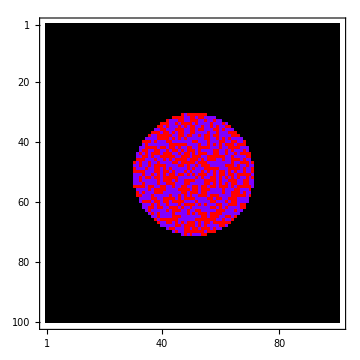

```mathematica
pltinitial=plt=MatrixPlot[A,ColorFunction->Hue,ColorRules->{0->Black},ImageSize->Medium]
```

#### CPM lattice

```mathematica
spCell=Flatten[
Map[(Values@ComponentMeasurements[MorphologicalComponents[#,CornerNeighbors->False],"Mask",CornerNeighbors->False])&,
Values@ComponentMeasurements[A,"Mask",CornerNeighbors->False]],
1];
```

```mathematica
spCellArr=<|MapIndexed[First[#2]->(First[#2]*#1)&,spCell]|>;
```

```mathematica
spCellArrU=Total[Values@spCellArr];
```

```mathematica
Colorize[spCellArrU,ImageSize->Medium]
```

-Graphics-

```mathematica
spTypeArr=Map[A Unitize[#]&,spCellArr];
```

```mathematica
spTypeArrU=Total[Values@spTypeArr];
```

```mathematica
Colorize[spTypeArrU,ImageSize->Medium]
```

-Graphics-

```mathematica
(*perimeter*)
perimeterPtsAssoc=<|
ParallelMap[Max[#]->Map[fun]@Position[ImageData@MorphologicalPerimeter[Image@#],1]&,
Values@spCellArr]|>;
```

```mathematica
Length/@perimeterPtsAssoc;
```

```mathematica
perimeterPts=Cases[Normal@perimeterPtsAssoc,{__Integer},{-2}];
```

```mathematica
boundaryPts["RemoveAll"];
boundaryPts["Insert",#]&/@perimeterPts;
```

```mathematica
celltypeAssoc=Max/@spTypeArr;
```

```mathematica
(* area and perimeter *)
```

```mathematica
areaAssoc=<|ComponentMeasurements[spCellArrU,"Count"]|>;
```

```mathematica
cellperimeter=<|ComponentMeasurements[spCellArrU,"PerimeterLength"]|>;
```

```mathematica
Counts@Extract[spCellArrU,Normal@boundaryPts]//KeySort
```

<|1→5,2→1,3→77,4→1,5→1,6→23,7→1,8→1,9→1,10→2,11→12,12→6,13→1,14→19,15→1,16→6,17→1,18→4,19→1,20→3,21→3,22→1,23→1,24→7,25→13,26→3,27→1,28→4,29→1,30→2,31→24,32→3,33→27,34→1,35→1,36→1,37→1,38→1,39→27,40→3,41→3,42→7,43→8,44→9,45→1,46→1,47→1,48→1,49→5,50→10,51→1,52→1,53→5,54→2,55→1,56→31,57→61,58→4,59→1,60→6,61→1,62→15,63→6,64→1,65→1,66→1,67→35,68→2,69→2,70→1,71→36,72→1,73→4,74→4,75→1,76→6,77→1,78→1,79→55,80→1,81→1,82→1,83→2,84→9,85→2,86→2,87→8,88→1,89→7,90→1,91→1,92→1,93→1,94→1,95→3,96→35,97→1,98→1,99→36,100→1,101→2,102→1,103→2,104→9,105→3,106→7,107→1,108→1,109→6,110→1,111→1,112→1,113→1,114→1,115→1,116→2,117→5,118→1,119→14,120→2,121→24,122→1,123→2,124→1,125→11,126→1,127→48,128→1,129→7,130→14,131→1,132→1,133→2,134→36,135→5,136→1,137→34,138→1,139→24,140→6,141→1,142→1,143→1,144→2,145→1,146→1,147→13,148→1,149→2,150→1,151→1,152→5,153→38,154→2,155→2,156→1,157→1,158→1,159→5,160→3,161→27,162→9,163→3,164→1,165→8,166→1,167→15,168→9,169→3,170→1,171→1,172→5,173→1,174→1,175→4,176→4,177→1,178→2,179→1,180→1,181→2,182→70,183→1,184→1,185→2,186→1,187→2,188→1,189→1,190→21,191→1,192→1,193→1,194→2,195→1|>

### simulate CPM

```mathematica
(* for area -> we will add -1 to areaAssoc[targetcellID]-- and do areaAssoc[sourcecellID]++ if sourcecellID is not background *)
```

```mathematica
ls["DropAll"];
```

```mathematica
Off[General::munfl];
Block[{t=0,T=T,neighbours,delt,targetpt,sourcept,sourceType,targetType,sourceCellId,targetCellId,
ΔE,neighbourCellIds,neighbourTypes,flag},
Monitor[
While[t≤MCSiter,
delt=0;
While[delt≤1,
flag=False;
delt+= 1.0/boundaryPts["Length"]; 
(* pick a random boundary pt and get its 4-neighbours for probable mutation *)
targetpt=RandomChoice[Normal@boundaryPts];
neighbours=crossneighbours[targetpt];
sourcept=RandomChoice@neighbours;

sourceType=spTypeArrU[[Sequence@@sourcept]];
sourceCellId=spCellArrU[[Sequence@@sourcept]];
targetType=spTypeArrU[[Sequence@@targetpt]];
targetCellId=spCellArrU[[Sequence@@targetpt]];
neighbourCellIds=Extract[spCellArrU,neighbours];
neighbourTypes=Extract[spTypeArrU,neighbours];
If[targetCellId≠sourceCellId,
(*compute the hamiltonian*)
ΔE=deltaH[sourceCellId,sourceType,targetCellId,targetType,neighbourCellIds,neighbourTypes];
If[ΔE<0,
(*accept the change*)
ls["Append",ΔE];
flag= True,
If[RandomReal[]≤Exp[-ΔE/T],
(*accept change with certain probability*)
ls["Append",ΔE];
flag=True
];
];
(*If flag is true then update area, perimeter and boundary pts*)
If[flag,
spTypeArrU[[Sequence@@targetpt]]=sourceType; (*copy type of the source in target pixel*)
spCellArrU[[Sequence@@targetpt]]=sourceCellId; (*copy the source cell number in target pixel*)
If[targetCellId≠0,areaAssoc[targetCellId]--];
If[areaAssoc[targetCellId]==0,KeyDropFrom[areaAssoc,targetCellId]];
If[sourceCellId≠ 0,areaAssoc[sourceCellId]++];
(*update boundary pts*)
updateBoundaryPts[sourceCellId,targetpt];
cellPerimeterUpdate[targetCellId,sourceCellId,neighbours];
];
];
];
plt=MatrixPlot[spTypeArrU,ColorFunction->Hue,ColorRules->{0->Black},ImageSize->Medium];
(*Export["C:\\Users\\aliha\\Desktop\\save\\"<>ToString[t]<>".jpg",plt];*)
t+=1;
],{t,plt}]
];
On[General::munfl];
```

### results

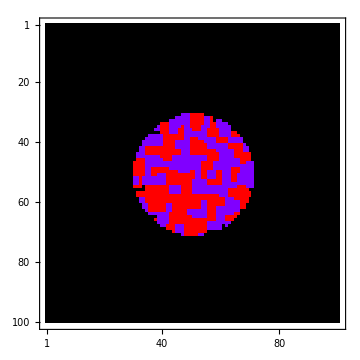
-Graphics--Graphics--Graphics-

```mathematica
Row[{pltinitial,MatrixPlot[spTypeArrU,ColorFunction->Hue,ColorRules->{0->Black},ImageSize->Medium],Colorize[spCellArrU,ImageSize->Medium]}]
```

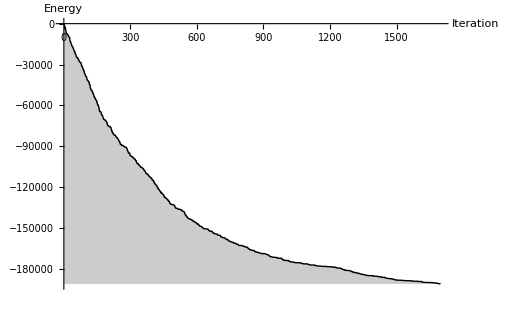

```mathematica
ListLinePlot[Accumulate[Normal@ls],PlotStyle->{Thick,Black},Filling->Bottom,
AxesStyle->Directive[Black,Bold, 12],AxesLabel->{"Iteration","Energy"},ImageSize->512,PlotRange->All]
```

```mathematica
Through[{#[0]&,
Apply[And]@*Map[Positive]@*Values,
Position[Values[#],0]/.{}->Missing&}[#]]&[KeySort@Counts@Extract[spCellArrU,Normal@boundaryPts]]
```

{Missing[KeyAbsent,0],True,Missing}

```mathematica
Function[x,x≥0,Listable]@cellperimeter//Apply[And]@*Values
```

True

```mathematica
keys=Keys@ComponentMeasurements[spCellArrU,"Label"];
```

```mathematica
masks=Unitize[Values@ComponentMeasurements[spCellArrU,"Mask"]];
```

```mathematica
types=If[#==1,1-> Blue,2-> Red]&@Max[spTypeArrU*#]&/@masks;
```

```mathematica
MapThread[Rasterize[HighlightImage[ColorReplace[Image[#],#2],{Green,"Boundary",Image@#1}],"Image",ImageSize->Medium]&,{masks,types}]//Total
```

-Graphics-